## Images

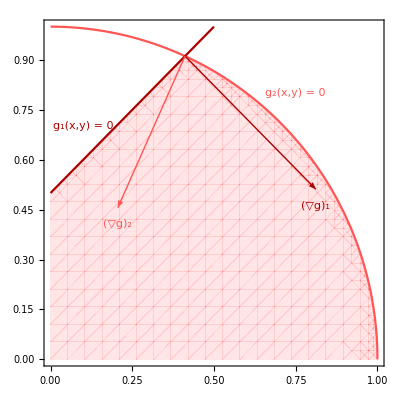

```mathematica
sol=NSolve[{x-y==-.5,x^2+y^2==1},{x,y}];
aa=x/.sol[[2]];
ba=y/.sol[[2]];
pp=Plot[{Sqrt[1-x^2],.5+x},{x,0,1},PlotRange->{0,1},AspectRatio->1,PlotStyle->{Lighter[Red],Darker[Red]}];
rp=RegionPlot[y≤x+.5&&y≤Sqrt[1-x^2],{x,0,1},{y,0,1},PlotStyle->{Red,Opacity[.1]},BoundaryStyle->None];ppp=Show[rp,pp,Graphics[{Darker[Red],Arrow[{{aa,ba},{aa+.4,ba-.4}}]}],Graphics[{Lighter[Red],Arrow[{{aa,ba},{aa-.5 aa,ba-.5 ba}}]}],Graphics[Text[Style["(▽g)_1",Large,Darker[Red]],{aa+.4,ba-.45}]],Graphics[Text[Style["(▽g)_2",Large,Lighter[Red]],{aa-.5 aa,ba-.5 ba-.05}]],Graphics[Text[Style["g_2(x,y) = 0",Lighter[Red],Medium],{0.75,0.8}]],Graphics[Text[Style["g_1(x,y) = 0",Darker[Red],Medium],{0.1,0.7}]]]
```

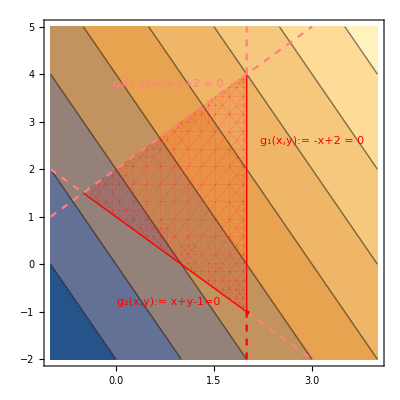

```mathematica
Show[ContourPlot[2 x+y,{x,-1,4},{y,-2,5}],RegionPlot[x+y≥1&& x-y≥-2&&-x≥-2,{x,-1,3},{y,-2,5},PlotStyle->{Red,Opacity[.1]},BoundaryStyle->None],Graphics[Text[Style["g_3(x,y):= x-y+2 = 0",Medium,Pink],{.8,3.8}]],Graphics[Text[Style["g_1(x,y):= -x+2 = 0",Medium,Red],{3,2.6}]],Graphics[Text[Style["g_2(x,y):= x+y-1=0",Medium,Red],{.8,-.8}]],ParametricPlot[{2,t},{t,-1,4},PlotStyle->{Red,Thick}],ParametricPlot[{2,t},{t,-2,-1},PlotStyle->{Red,Dashed}],ParametricPlot[{2,t},{t,4,5},PlotStyle->{Pink,Dashed}],ParametricPlot[{t,1-t},{t,-1,-.5},PlotStyle->{Pink,Dashed}],
ParametricPlot[{t,1-t},{t,-.5,2},PlotStyle->{Red,Thick}],
ParametricPlot[{t,1-t},{t,2,3},PlotStyle->{Pink,Dashed}],ParametricPlot[{t,t+2},{t,-1,3},PlotStyle->{Pink,Dashed}],Graphics[{PointSize->Large,Red,Point[{2,-1}]}],FrameLabel->{TextCell["Working-set in red",Red,Large]}]
```

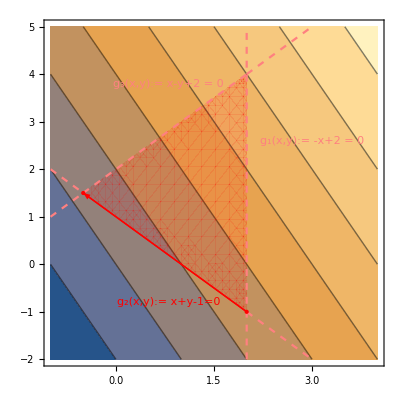

```mathematica
Show[ContourPlot[2 x+y,{x,-1,4},{y,-2,5}],RegionPlot[x+y≥1&& x-y≥-2&&-x≥-2,{x,-1,3},{y,-2,5},PlotStyle->{Red,Opacity[.1]},BoundaryStyle->None],Graphics[Text[Style["g_3(x,y):= x-y+2 = 0",Medium,Pink],{.8,3.8}]],Graphics[Text[Style["g_1(x,y):= -x+2 = 0",Medium,Pink],{3,2.6}]],Graphics[Text[Style["g_2(x,y):= x+y-1=0",Medium,Red],{.8,-.8}]],ParametricPlot[{2,t},{t,-2,5},PlotStyle->{Pink,Dashed}],Graphics[{Red, Arrowheads[Large],Arrow[{{2,-1},{-1/2,3/2}}]}],ParametricPlot[{t,t+2},{t,-1,-1/2},PlotStyle->{Pink,Dashed}],ParametricPlot[{t,t+2},{t,2,3},PlotStyle->{Pink,Dashed}],ParametricPlot[{t,1-t},{t,-1,-.5},PlotStyle->{Pink,Dashed}],
ParametricPlot[{t,1-t},{t,-.5,2},PlotStyle->{Red,Thick}],
ParametricPlot[{t,1-t},{t,2,3},PlotStyle->{Pink,Dashed}],ParametricPlot[{t,t+2},{t,-1/2,2},PlotStyle->{Pink,Dashed}],Graphics[{PointSize->Large,Red,Point[{2,-1}]}],Graphics[{PointSize->Large,Red,Point[{-1/2,3/2}]}],FrameLabel->{TextCell["Working-set in red",Red,Large]}]
```

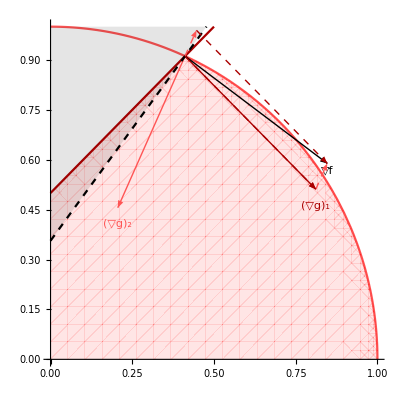

```mathematica
NSolve[{x-y==-.5,x^2+y^2==1},{x,y}]
```

{{x→-0.911438,y→-0.411438},{x→0.411438,y→0.911438}}

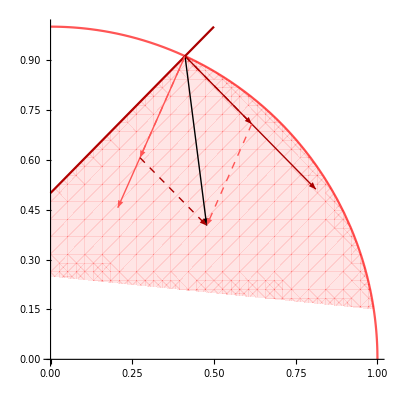
```mathematica
Show[-Graphics-,Graphics[Text[Style["g_3(x,y) = 0",Darker[Red],Medium],{0.4,0.15}]],Graphics[Text[Style["g_2(x,y) = 0",Lighter[Red],Medium],{0.75,0.8}]],Graphics[Text[Style["(▽g)_1",Large,Darker[Red]],{aa+.4,ba-.45}]],Graphics[Text[Style["(▽g)_2",Large,Lighter[Red]],{aa-.5 aa,ba-.5 ba-.05}]],Graphics[Text[Style["g_1(x,y) = 0",Darker[Red],Medium],{0.1,0.7}]],Plot[.25-.1x,{x,0,1},PlotRange->{0,1},PlotStyle->Red,AspectRatio->1],Graphics[Text[Style["▽f",Large],{.475,.35}]]]
```

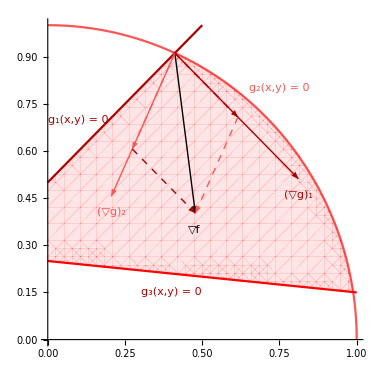

```mathematica
NSolve[{x-y==-.5,x^2+y^2==1},{x,y}]
```

{{x→-0.911438,y→-0.411438},{x→0.411438,y→0.911438}}

## Animated objective gradient

```mathematica
Manipulate[Show[ppp,Graphics[Arrow[{{aa,ba},u}],RegionPlot[y≤x+.5,{x,0,1},{y,0,1}]],Plot[-(u[[1]]-aa)/(u[[2]]-ba) (x-aa)+ba,{x,0,1},PlotStyle->{Dashed,Black},PlotRange->{0,1},Filling->If[u[[2]]≤ba,Top,Bottom],FillingStyle->Opacity[0.1]],Graphics[Text[Style["▽f",Large],{u[[1]],u[[2]]-.1}]]],{{u,{.5,.2}},Locator},Initialization:>(sol=NSolve[{x-y==-.5,x^2+y^2==1},{x,y}];
aa=x/.sol[[2]];
ba=y/.sol[[2]];
pp=Plot[{Sqrt[1-x^2],.5+x},{x,0,1},PlotRange->{0,1},AspectRatio->1,PlotStyle->{Lighter[Red],Darker[Red]}];
rp=RegionPlot[y≤x+.5&&y≤Sqrt[1-x^2],{x,0,1},{y,0,1},PlotStyle->{Red,Opacity[.1]},BoundaryStyle->None];ppp=Show[pp,rp,Graphics[{Darker[Red],Arrow[{{aa,ba},{aa+.4,ba-.4}}]}],Graphics[Text[Style["(▽g)_1",Large,Darker[Red]],{aa+.4,ba-.45}]],Graphics[Text[Style["(▽g)_2",Large,Lighter[Red]],{aa-.5 aa,ba-.5 ba-.05}]],Graphics[{Lighter[Red],Arrow[{{aa,ba},{aa-.5 aa,ba-.5 ba}}]}]];)]
```

The shaded side of the dotted line shows descent directions for the objective function f.

## Between vectors: λ1 (▽g)_1+ λ2 (▽g)_2

```mathematica
Manipulate[Show[ppp,Graphics[{Black,Arrow[{{aa,ba},{aa,ba}+λ1{.4,-.4}+λ2{-.5 aa,-.5 ba}}]}],Graphics[{Lighter[Red],Dashed,Arrow[{{aa,ba},{aa-λ2 .5 aa,ba-λ2 .5ba}}]}],Graphics[{Lighter[Red],Dashed,Arrow[{{aa+λ1 .4,ba-λ1 .4},{aa,ba}+λ1{.4,-.4}+λ2{-.5 aa,-.5 ba}}]}],Graphics[Text[Style["▽f",Large],{aa,ba}+λ1{.4,-.4}+λ2{-.5 aa,-.5 ba}+{0,-.02}]],Graphics[{Darker[Red],Dashed,Arrow[{{aa-λ2 .5 aa,ba-λ2 .5 ba},{aa,ba}+λ1{.4,-.4}+λ2{-.5 aa,-.5 ba}}]}],Graphics[{Darker[Red],Dashed,Arrow[{{aa,ba},{aa+λ1 .4,ba-λ1 .4}}]}]],{{λ1,1},-1,1},{{λ2,1},-1,1},Initialization:>(sol=NSolve[{x-y==-.5,x^2+y^2==1},{x,y}];
aa=x/.sol[[2]];
ba=y/.sol[[2]];
pp=Plot[{Sqrt[1-x^2],.5+x},{x,0,1},PlotRange->{0,1},AspectRatio->1,PlotStyle->{Lighter[Red],Darker[Red]}];
rp=RegionPlot[y≤x+.5&&y≤Sqrt[1-x^2],{x,0,1},{y,0,1},PlotStyle->{Red,Opacity[.1]},BoundaryStyle->None];ppp=Show[pp,rp,Graphics[{Darker[Red],Arrow[{{aa,ba},{aa+.4,ba-.4}}]}],Graphics[Text[Style["(▽g)_1",Large,Darker[Red]],{aa+.4,ba-.45}]],Graphics[Text[Style["(▽g)_2",Large,Lighter[Red]],{aa-.5 aa,ba-.5 ba-.05}]],Graphics[{Lighter[Red],Arrow[{{aa,ba},{aa-.5 aa,ba-.5 ba}}]}]];)]
```

## Multiplier Check

```mathematica
Manipulate[Show[ppp,Graphics[{Black,Arrow[{{aa,ba},{aa,ba}+λ1{.4,-.4}+λ2{-.5 aa,-.5 ba}}]}],Plot[-(.4*λ1-.5*λ2*aa)/(-.4*λ1-.5*λ2*ba) (x-aa)+ba,{x,0,1},PlotStyle->{Dashed,Black},PlotRange->{0,1},Filling->If[-.4*λ1-.5*λ2*ba+ba≤ba,Top,Bottom],FillingStyle->Opacity[0.1]],Graphics[{Lighter[Red],Dashed,Arrow[{{aa,ba},{aa-λ2 .5 aa,ba-λ2 .5ba}}]}],Graphics[{Lighter[Red],Dashed,Arrow[{{aa+λ1 .4,ba-λ1 .4},{aa,ba}+λ1{.4,-.4}+λ2{-.5 aa,-.5 ba}}]}],
Graphics[Text[Style["▽f",Large],{aa,ba}+λ1{.4,-.4}+λ2{-.5 aa,-.5 ba}+{0,-.02}]],Graphics[{Darker[Red],Dashed,Arrow[{{aa-λ2 .5 aa,ba-λ2 .5 ba},{aa,ba}+λ1{.4,-.4}+λ2{-.5 aa,-.5 ba}}]}],Graphics[{Darker[Red],Dashed,Arrow[{{aa,ba},{aa+λ1 .4,ba-λ1 .4}}]}]],{{λ1,1},-1,1},{{λ2,1},-1,1},Initialization:>(sol=NSolve[{x-y==-.5,x^2+y^2==1},{x,y}];
aa=x/.sol[[2]];
ba=y/.sol[[2]];
pp=Plot[{Sqrt[1-x^2],.5+x},{x,0,1},PlotRange->{0,1},AspectRatio->1,PlotStyle->{Lighter[Red],Darker[Red]}];
rp=RegionPlot[y≤x+.5&&y≤Sqrt[1-x^2],{x,0,1},{y,0,1},PlotStyle->{Red,Opacity[.1]},BoundaryStyle->None];ppp=Show[pp,rp,Graphics[{Darker[Red],Arrow[{{aa,ba},{aa+.4,ba-.4}}]}],Graphics[Text[Style["(▽g)_1",Large,Darker[Red]],{aa+.4,ba-.45}]],Graphics[Text[Style["(▽g)_2",Large,Lighter[Red]],{aa-.5 aa,ba-.5 ba-.05}]],Graphics[{Lighter[Red],Arrow[{{aa,ba},{aa-.5 aa,ba-.5 ba}}]}]];)]
```

## Group Problem 2

```mathematica
Show[-Graphics-,Graphics[Text[Style["g_3(x,y) = 0",Darker[Red],Medium],{0.4,0.15}]],Graphics[Text[Style["g_2(x,y) = 0",Lighter[Red],Medium],{0.75,0.8}]],Graphics[Text[Style["(▽g)_1",Large,Darker[Red]],{aa+.4,ba-.45}]],Graphics[Text[Style["(▽g)_2",Large,Lighter[Red]],{aa-.5 aa,ba-.5 ba-.05}]],Graphics[Text[Style["g_1(x,y) = 0",Darker[Red],Medium],{0.1,0.7}]],Plot[.25-.1x,{x,0,1},PlotRange->{0,1},PlotStyle->Red,AspectRatio->1],Graphics[Text[Style["▽f",Large],{.475,.35}]]]
```

-Graphics-